# CFD Convergence Testing

Looking at CFD operator convergence factor over time.

```mathematica
Clear["`*"];
```

## Essential Modules and Initializations

### Defining Coefficients

```mathematica
Clear[coeffP12,coeffP6,coeffP8,coeffT4,coeffT6,coeffP10,coeffT8,coeffT42D];

coeffVariables={
α,β,
α12,β12,
α21,α22,β22,
β31,α31,α32,β32,
β41,α41,α42,β42,
a,b,c,d,
a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1,
a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2,
a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3,
a4,b4,c4,d4,e4,f4,g4,h4,i4,j4,k4
};
coeffAllZero={
α->0,β->0,
α12->0,β12->0,
α21->0,α22->0,β22->0,
β31->0,α31->0,α32->0,β32->0,
β41->0,α41->0,α42->0,β42->0,
a->0,b->0,c->0,d->0,
a1->0,b1->0,c1->0,d1->0,e1->0,f1->0,g1->0,h1->0,i1->0,j1->0,k1->0,
a2->0,b2->0,c2->0,d2->0,e2->0,f2->0,g2->0,h2->0,i2->0,j2->0,k2->0,
a3->0,b3->0,c3->0,d3->0,e3->0,f3->0,g3->0,h3->0,i3->0,j3->0,k3->0,
a4->0,b4->0,c4->0,d4->0,e4->0,f4->0,g4->0,h4->0,i4->0,j4->0,k4->0
};

coeffNJP8=Join[{a->40/27,b->25/54,α->4/9,β->1/36,a1->-79/20,b1->-77/5,c1->55/4,d1->20/3,e1->-5/4,f1->1/5,g1->-1/60,a2->-257/1080,b2->-107/60,c2->-5/24,d2->55/27,e2->5/24,f2->-1/60,g2->1/1080,a3->-34/675,b3->-127/225,c3->-7/12,d3->20/27,e3->4/9,f3->1/75,g3->-1/2700,a4->-1/600,b4->-101/600,c4->-17/24,d4->0,e4->17/24,f4->101/600,g4->1/600,α12->12,β12->15,α21->1/18,α22->5/2,β22->10/9,β31->1/90,α31->4/15,α32->8/9,β32->1/6,β41->1/20,α41->1/2,α42->1/2,β42->1/20},coeffAllZero];

coeffT4=Join[{α->1/4,α12->3,a->3/2,a1->-17/6,b1->3/2,c1->3/2,d1->-1/6},coeffAllZero];

coeffT42D=Join[{α->1/10,α12->10,a->6/5,a1->145/12,b1->-76/3,c1->29/2,d1->-4/3,e1->1/12},coeffAllZero];



coeffT6=Join[{
α->1/3,
α12->5,
α21->1/8,α22->3/4,
a->14/9,b->1/9,c->0,d->0,
a1->-197/60,b1->-5/12,c1->5,d1->-5/3,e1->5/12,f1->-1/20,
a2->-43/96,b2->-5/6,c2->9/8,d2->1/6,e2->-1/96
},coeffAllZero];

coeffT8=Join[{
α->3/8,
α12->7,
α21->1/12,α22->5/4,
α31->13/55,α32->6/11,
a->25/16,b->1/5,c->-1/80,
a1->-503/140,b1->-63/20,c1->21/2,d1->-35/6,e1->35/12,f1->-21/20,g1->7/30,h1->-1/42,
a2->-79/240,b2->-77/60,c2->55/48,d2->5/9,e2->-5/48,f2->1/60,g2->-1/720,
a3->-1/66,b3->-2051/3300,c3->-53/132,d3->31/33,e3->7/66,f3->-1/132,g3->1/3300
},coeffAllZero];


coeffP6=Join[{
α->17/57,β->-1/114,
α12->8,β12->6,
a->30/19,b->0,c->0,d->0,
a1->-43/12,b1->-20/3,c1->9,d1->4/3,e1->-1/12
},coeffAllZero];

coeffP8=Join[{
α->4/9,β->1/36,
α12->12,β12->15,
α21->2,α22->2/3,β22->1/15,
a->40/27,b->25/54,
a1->-79/20,b1->-77/5,c1->55/4,d1->20/3,e1->-5/4,f1->1/5,g1->-1/60,
a2->-247/900,b2->-19/12,c2->1/3,d2->13/9,e2->1/12,f2->-1/300
},coeffAllZero];

coeffP10={
α->1/2,β->1/20,
α12->16,β12->28,
α21->1/21,α22->3,β22->5/3,
β31->1/90,α31->4/15,α32->8/9,β32->1,
β41->0,α41->0,α42->0,β42->0,
a->17/12,b->101/150,c->1/100,d->0,
a1->-1181/280,b1->-892/35,c1->77/5,d1->56/3,e1->-35/6,f1->28/15,g1->-7/15,h1->8/105,i1->-1/168,j1->0,k1->0,
a2->-544/2581,b2->-39/20,c2->-17/20,d2->95/36,e2->5/12,f2->-1/20,g2->1/180,h2->-1/2940,i2->0,j2->0,k2->0,
a3->-34/675,b3->-127/225,c3->-7/12,d3->20/27,e3->4/9,f3->1/75,g3->-1/2700,h3->0,i3->0,j3->0,k3->0,
a4->0,b4->0,c4->0,d4->0,e4->0,f4->0,g4->0,h4->0,i4->0,j4->0,k4->0
};

coeffP12={
α->8/15,β->1/15,
α12->20,β12->45,
α21->1/27,α22->4,β22->28/9,
β31->1/168,α31->4/21,α32->4/3,β32->5/12,
β41->1/42,α41->1/3,α42->5/6,β42->1/6,
a->308/225,b->182/225,c->4/175,d->-1/1575,
a1->-1590/359,b1->-4609/126,c1->711/56,d1->40,e1->-35/2,f1->42/5,g1->-7/2,h1->8/7,i1->-15/56,j1->5/126,k1->-1/360,
a2->-857/4963,b2->-621/280,c2->-83/35,d2->511/135,e2->7/6,f2->-7/30,g2->7/135,h2->-1/105,i2->1/840,j2->-1/13608,k2->0,
a3->-115/4024,b3->-1019/2205,c3->-19/20,d3->23/45,e3->125/144,f3->1/15,g3->-1/180,h3->1/2205,i3->-1/47040,j3->0,k3->0,
a4->-1/1680,b4->-193/2205,c4->-107/180,d4->-9/20,e4->25/36,f4->19/45,g4->1/60,h4->-1/1260,i4->1/35280,j4->0,k4->0
};
```

### LHS and RHS Matrix Modules

```mathematica
LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32},
{0,β41,α41,1,α42,β42},
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1},
{a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2},
{a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3},
{a4,b4,c4,d4,e4,f4,g4,h4,i4,j4,k4}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
]

InsideOneSidedBoundaryLHS[M_,row_,borders_,coeff_]:=Module[{newM,size=Length[M]},
newM=M;

For[i=1,i<=borders,i++,
newM[[row+i-1]]=ConstantArray[0,size];
newM[[row-i]]=ConstantArray[0,size];
For[j=1,j<=Length[LHSBorders[[i]]],j++,
newM[[row+i-1,j+row-1]]=LHSBorders[[i,j]]/.coeff;
newM[[row-i,row-j]]=LHSBorders[[i,j]]/.coeff;
]
];

newM[[row+1,row-1]]=0;
newM[[row+2,row-1]]=0;
newM[[row+1,row-2]]=0;

newM[[row-2,row]]=0;
newM[[row-3,row]]=0;
newM[[row-2,row+1]]=0;

newM
]

PeriodicLHS[size_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β,
Band[{1,size}]->α,
Band[{1,size-1}]->β,
Band[{size,1}]->α,
Band[{size-1,1}]->β
}/.coeff,{size,size}];
M
]

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a/2,
Band[{3,1}]->-b/4,
Band[{4,1}]->-c/6,
Band[{5,1}]->-d/8,
Band[{1,2}]->a/2,
Band[{1,3}]->b/4,
Band[{1,4}]->c/6,
Band[{1,5}]->d/8
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]


RHSMatrix2D[size_,borders_,coeff_,H_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->-2(a+b 1/4+c 1/9+d 1/16),
Band[{2,1}]->a,
Band[{3,1}]->b/(4),
Band[{4,1}]->c/(9),
Band[{5,1}]->d/(16),
Band[{1,2}]->a,
Band[{1,3}]->b/(4),
Band[{1,4}]->c/(9),
Band[{1,5}]->d/(16)
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]

InsideOneSidedBoundaryRHS[M_,row_,borders_,coeff_]:=Module[{newM,size=Length[M]},
newM=M;

For[i=1,i<=borders,i++,
newM[[row+i-1]]=ConstantArray[0,size];
newM[[row-i]]=ConstantArray[0,size];
For[j=1,j<=Length[RHSBorders[[i]]],j++,
newM[[row+i-1,j+row-1]]=RHSBorders[[i,j]]/.coeff;
newM[[row-i,row-j]]=-RHSBorders[[i,j]]/.coeff;
]
];

newM[[row+1,row-1]]=0;
newM[[row+2,row-1]]=0;
newM[[row+3,row-1]]=0;
newM[[row+1,row-2]]=0;
newM[[row+2,row-2]]=0;
newM[[row+1,row-3]]=0;

newM[[row-2,row]]=0;
newM[[row-3,row]]=0;
newM[[row-4,row]]=0;
newM[[row-2,row+1]]=0;
newM[[row-3,row+1]]=0;
newM[[row-2,row+2]]=0;

newM
]

PeriodicRHS[size_,coeff_]:=Module[{M,H},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a/2,
Band[{3,1}]->-b/4,
Band[{4,1}]->-c/6,
Band[{5,1}]->-d/8,
Band[{1,2}]->a/2,
Band[{1,3}]->b/4,
Band[{1,4}]->c/6,
Band[{1,5}]->d/8,
Band[{1,size}]->-a/2,
Band[{1,size-1}]->-b/4,
Band[{1,size-2}]->-c/6,
Band[{1,size-3}]->-d/8,
Band[{size,1}]->a/2,
Band[{size-1,1}]->b/4,
Band[{size-2,1}]->c/6,
Band[{size-3,1}]->d/8
}/.coeff,{size,size}];

M
]

DirichletBoundary[M_,LeftHandSide_,left_,right_]:=Module[{newM,size},
newM=M;
size=Length[newM[[1]]];
If[left,newM[[1]]=ConstantArray[0,size]];
If[right,newM[[size]]=ConstantArray[0,size]];
newM=Transpose[newM];
If[left,newM[[1]]=ConstantArray[0,size]];
If[right,newM[[size]]=ConstantArray[0,size]];
newM=Transpose[newM];
If[LeftHandSide,
If[left,newM[[1,1]]=1];
If[right,newM[[size,size]]=1];
];
newM
]



(*L=LHSMatrix[12,3,{}];
DirichletBoundary[L,True,True,False]//MatrixForm
RHSMatrix[12,3,{d->0}];
DirichletBoundary[%,False,True,False]//MatrixForm

LHSMatrix[12,1,{}]//MatrixForm;
RHSMatrix2D[12,1,{}]/11^2//MatrixForm;*)

l=PeriodicLHS[25,{}];
r=PeriodicRHS[25,{}];
l=InsideOneSidedBoundaryLHS[l,12,1,{}];
r=InsideOneSidedBoundaryRHS[r,12,1,{}];
l//MatrixForm
r//MatrixForm
```

(1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α
α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β
β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β12 | α12 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | α12 | β12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β
β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α
α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | 1)

(0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2
-a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4
-b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6
-c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8
-d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-k1 | -j1 | -i1 | -h1 | -g1 | -f1 | -e1 | -d1 | -c1 | -b1 | -a1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a1 | b1 | c1 | d1 | e1 | f1 | g1 | h1 | i1 | j1 | k1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6 | d/8
d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4 | c/6
c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2 | b/4
b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0 | a/2
a/2 | b/4 | c/6 | d/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d/8 | -c/6 | -b/4 | -a/2 | 0)

### Advection Equation Setup

```mathematica
Clear[Δt,waveSpeed];

(*Initialize Parameters*)
Δt=0.0001;
waveSpeed=0.05;
```

## Convergence Testing

### Setting Up The Operators

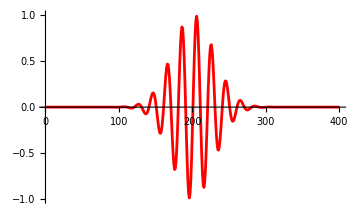

```mathematica
Clear[ϕ1,ϕ2,ϕ3,coeffToUse];

(* Coefficients *)
coeffToUse=coeffNJP8;
(* Initial Condition *)
f[x_]:=Exp[-(10x-10/2)^2]Sin[40π x];
(*f[x_]:=Sin[10π x];*)

(**************************************************************************************)

(* Define the Initial Conditions with n=400,200,100 for each function *)
(* h: n=400 *)
n1=401;

(* 2h: n=200 *)
n2=201;

(* 4h: n=100 *)
n3=101;

(* This will reset the initial conditions *)
Reset[]:=Module[{},
ϕ1=Array[f[#]&,n1,{0,1}];
ϕ2=Array[f[#]&,n2,{0,1}];
ϕ3=Array[f[#]&,n3,{0,1}];
];
Reset[];

(* Setting up the Derivative Operators based on the LHS and RHS matrices and the precalculated Inverses *)
(* Set up Derivative Operator Q1 *)
LHS1=PeriodicLHS[n1,coeffToUse];
RHS1=PeriodicRHS[n1,coeffToUse];
RHS1=(n1-1)RHS1;
Q1=Inverse[LHS1].RHS1;
ctQ1=waveSpeed Δt Q1;

(* Set up Derivative Operator Q2 *)
LHS2=PeriodicLHS[n2,coeffToUse];
RHS2=PeriodicRHS[n2,coeffToUse];
RHS2=(n2-1)RHS2;
Q2=Inverse[LHS2].RHS2;
ctQ2=waveSpeed Δt Q2;

(* Set up Derivative Operator Q3 *)
LHS3=PeriodicLHS[n3,coeffToUse];
RHS3=PeriodicRHS[n3,coeffToUse];
RHS3=(n3-1)RHS3;
Q3=Inverse[LHS3].RHS3;
ctQ3=waveSpeed Δt Q3;

(* This module calculates the convergence factor between the functions at points that are common to all of them *)
GetQ[]:=Module[{ϕ1a,ϕ2a},
ϕ1a=Table[ϕ1[[4i-3]],{i,1,n3}];
ϕ2a=Table[ϕ2[[2i-1]],{i,1,n3}];
If[Norm[ϕ2a-ϕ1a]!=0,Norm[ϕ3-ϕ2a]/Norm[ϕ2a-ϕ1a],0]//N
];

ListPlot[ϕ1,Joined->True,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Red]

(*GetQ[]*)

(*ϕ1a2=Table[ϕ1[[4i-3]],{i,1,n3}];
ϕ2a2=Table[ϕ2[[2i-1]],{i,1,n3}];
Show[ListPlot[ϕ1a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Red],
ListPlot[ϕ2a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Green],
ListPlot[ϕ3,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Blue]
]*)
```

### Running the Operators

```mathematica
Clear[Q,ϕ1graph,ϕ2graph,ϕ3graph];

(* Reset to initial conditions *)
Reset[];

(* Initialize the data collection for plotting *)
Q={};
ϕ1graph={};
ϕ2graph={};
ϕ3graph={};

(* This loop runs for every step and will update the functions based on the derivative operators *)
For[i=0,i<20/Δt,i++,
(* Update the functions *)
ϕ1=ϕ1-ctQ1.ϕ1;
ϕ2=ϕ2-ctQ2.ϕ2;
ϕ3=ϕ3-ctQ3.ϕ3;

(* Collect data points every 1000 steps *)
If[Mod[i,1000]==0,
AppendTo[Q,GetQ[]];
AppendTo[ϕ1graph,ListPlot[ϕ1,Joined->True,PlotRange->{-1,1}]];AppendTo[ϕ2graph,ListPlot[ϕ2,Joined->True,PlotRange->{-1,1}]];
AppendTo[ϕ3graph,ListPlot[ϕ3,Joined->True,PlotRange->{-1,1}]];
];
];
```

### Plotting Results

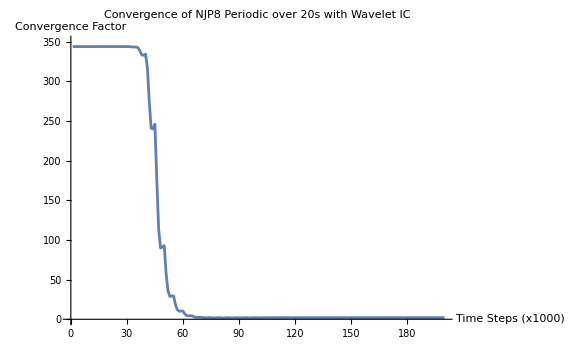

```mathematica
(*ListAnimate[ϕ1graph,ImageSize->Medium]
ListAnimate[ϕ2graph,ImageSize->Medium]
ListAnimate[ϕ3graph,ImageSize->Medium]*)

(*ListPlot[ϕ1,Joined->True,ImageSize->Medium]
ListPlot[ϕ2,Joined->True,ImageSize->Medium]
ListPlot[ϕ3,Joined->True,ImageSize->Medium]*)

(*ϕ1graph[[50]]
ϕ2graph[[50]]
ϕ3graph[[50]]*)

(* Plot the convergence Factor *)
ListPlot[Q,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of NJP8 Periodic over 20s with Wavelet IC",PlotRange->{0,350}]
```

```mathematica
2^8
```

256

### Saved Data

```mathematica
Q
```

{18.8624,18.8621,18.8615,18.8604,18.8589,18.857,18.8547,18.8521,18.849,18.8455,18.8416,18.8373,18.8327,18.8276,18.8221,18.8162,18.81,18.8033,18.7962,18.7888,18.7809,18.7727,18.7641,18.755,18.7456,18.7358,18.7256,18.715,18.7041,18.6927,18.681,18.6688,18.6563,18.6435,18.6302,18.6166,18.6026,18.5882,18.5734,18.5583,18.5428,18.5269,18.5107,18.4941,18.4771,18.4598,18.4421,18.424,18.4056,18.3869,18.3676,18.3477,18.3274,18.3072,18.2869,18.2646,18.2394,18.2139,18.1922,18.1709,18.1373,18.0866,18.0394,18.0186,17.9979,17.906,17.7346,17.6014,17.5986,17.576,17.2425,16.6659,16.3142,16.3896,16.3284,15.3919,14.1354,13.5758,13.7916,13.6124,12.1105,10.6269,10.1655,10.4555,10.1693,8.76127,7.6641,7.45606,7.72174,7.4196,6.42399,5.78293,5.77061,5.97882,5.71099,5.07095,4.74559,4.83845,4.98709,4.76839,4.37368,4.238,4.36676,4.46178,4.29706,4.06915,4.03823,4.15825,4.21061,4.10018,3.98508,4.00304,4.0921,4.1162,4.05379,4.009,4.04028,4.09483,4.10441,4.07712,4.06834,4.09448,4.12268,4.12704,4.11972,4.12379,4.14,4.15304,4.15627,4.15717,4.16295,4.17158,4.17773,4.18072,4.1836,4.18795,4.1925,4.19592,4.19849,4.20112,4.20398,4.20661,4.2088,4.21074,4.21262,4.21441,4.216,4.21738,4.21861,4.21972,4.22069,4.2215,4.22217,4.2227,4.22309,4.22334,4.22346,4.22344,4.22329,4.22301,4.2226,4.22206,4.22139,4.2206,4.21968,4.21863,4.21747,4.21618,4.21477,4.21325,4.2116,4.20984,4.20797,4.20598,4.20388,4.20167,4.19935,4.19692,4.19438,4.19174,4.18899,4.18614,4.18319,4.18014,4.17698,4.17373,4.17038,4.16694,4.1634,4.15977,4.15604,4.15223,4.14833,4.14433,4.14025,4.13609,4.13183,4.1275,4.12308,4.11858}

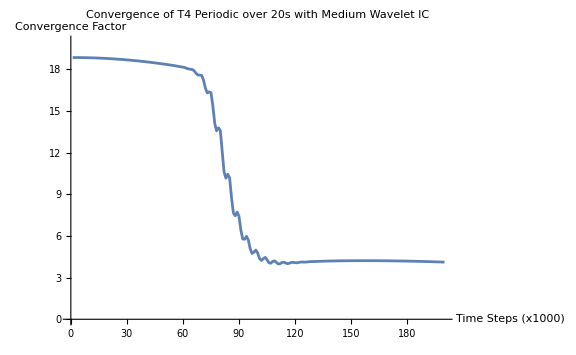

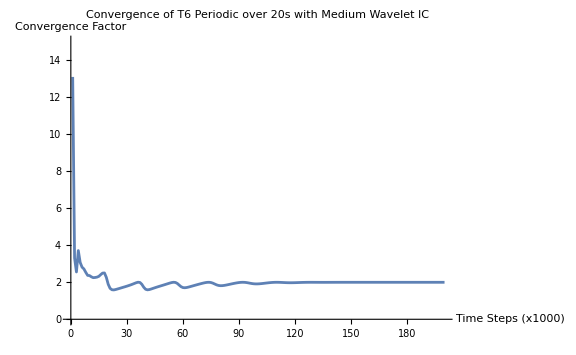

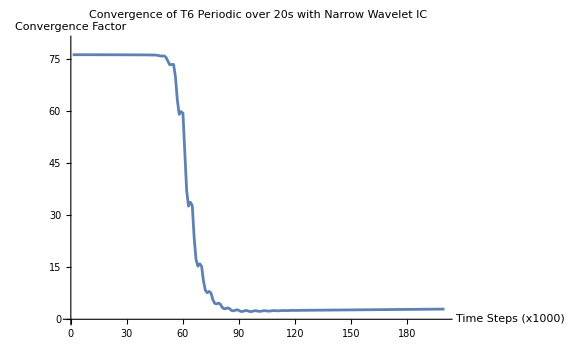

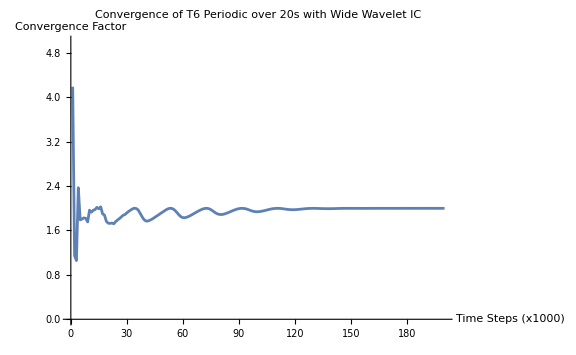

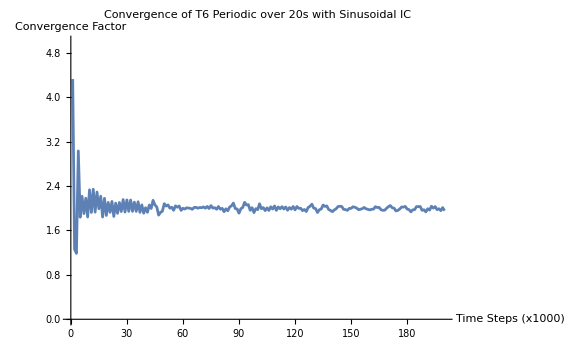

```mathematica
QT4Wavelet={18.862397902077085,18.862124894139704,18.861450603498483,18.86037504722157,18.858898288804436,18.857020437645726,18.854741649042186,18.852062124103245,18.848982109698934,18.845501898439036,18.841621828563106,18.83734228379638,18.8326636933716,18.827586531747105,18.822111318613903,18.81623861866671,18.80996904147373,18.80330324129737,18.7962419169161,18.788785811440007,18.780935712016667,18.77269244979936,18.764056899449415,18.75502997913271,18.745612650261098,18.735805916625754,18.725610825132637,18.715028464577866,18.704059966697184,18.6927065046761,18.680969289308532,18.66884957166438,18.656348648879646,18.643467871507394,18.630208617994324,18.616572243780745,18.60256011136486,18.588173770812634,18.57341503589829,18.558285468076765,18.54278558955441,18.526915626141385,18.510678502154434,18.49408035381292,18.477122066113406,18.45978946699192,18.442067341776095,18.42397845184218,18.405579621886826,18.38685199845077,18.36761016287529,18.34769960954596,18.32739190278776,18.307225100849937,18.28688864484613,18.264642647320958,18.239431876827016,18.213934676429698,18.192201302978802,18.170886566085084,18.137293251170775,18.08664824679029,18.039383243790986,18.01858655829918,17.997897532604735,17.906048529113367,17.734642104356386,17.6013570642417,17.598587995867724,17.575982531591748,17.24252833546232,16.665935618005665,16.31423408459767,16.389567963443373,16.328445228407475,15.391900196958202,14.135394241670486,13.575800434030896,13.791601554096893,13.612448677406185,12.110536580415292,10.626928383925133,10.165521669583152,10.455479410324736,10.169329799570622,8.76126870449608,7.664099176573466,7.456056904133408,7.721744419609171,7.419598915273023,6.423986733389704,5.7829303852448675,5.770613969473116,5.978820537791952,5.710985369114031,5.070949633504911,4.745585187911925,4.8384549946982816,4.987092518431363,4.768392389019898,4.373677741975792,4.238004105958128,4.36676322947874,4.461782860721652,4.297064600376818,4.069148376973621,4.038232205260603,4.15824630924455,4.210607189952284,4.100176452418755,3.9850798517620194,4.003038971712773,4.092100967763937,4.116195717613846,4.0537921423551895,4.008998860867858,4.040275663730188,4.094826113983542,4.104410960920677,4.077124058643775,4.06833625537772,4.094483918666642,4.1226804595444655,4.127041486814571,4.119723324260738,4.123793495719931,4.140002189080828,4.153039841943709,4.156271137780436,4.1571687908851445,4.162954408900778,4.171581872741332,4.17773030830218,4.180716763461467,4.183603800063522,4.18795154900579,4.192504605550622,4.195920303753791,4.198492499932552,4.201124662747672,4.203976385438189,4.206608450170017,4.20880287816846,4.210744771729638,4.212623323899662,4.214407608557381,4.215995226573581,4.2173778792228855,4.218611632681131,4.219721556259375,4.220690135695139,4.221503093229336,4.222167945950797,4.2226961329285775,4.223089208466796,4.2233441090417525,4.2234612112627925,4.223443826031729,4.223294289474465,4.2230133053009675,4.222601621034085,4.222060713147024,4.221392181955812,4.220597320724268,4.219677299175793,4.218633392335474,4.217466946246521,4.216179273149386,4.214771647057907,4.213245347553823,4.211601669380228,4.209841905565536,4.207967340560175,4.205979255750202,4.203878933024381,4.201667652840108,4.199346692315154,4.196917325554585,4.1943808241879195,4.1917384572467835,4.1889914906431,4.186141187080152,4.183188805999357,4.180135603480644,4.176982832094844,4.173731740723999,4.170383574517585,4.166939574712687,4.163400978571934,4.159769019225448,4.156044925592861,4.152229922255492,4.148325229349108,4.144332062491233,4.140251632626867,4.136085145983157,4.131833803931501,4.127498802928203,4.12308133438228,4.118582584603011};
ListPlot[QT4Wavelet,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of T4 Periodic over 20s with Medium Wavelet IC",PlotRange->{0,20}]

QT6WaveletMedium={13.098227360862,3.3072287197420067,2.556974067126167,3.7138210670159344,3.072246536535872,2.8169639072124957,2.7200492632770503,2.534371980488348,2.3721364592055334,2.3611414679657647,2.293259899194157,2.248653269027188,2.2581693833999568,2.2776380529122595,2.3212212752595325,2.414778474616011,2.4962967582854914,2.5035792928257026,2.2644511738211928,1.8927928817904849,1.6724766906357316,1.5957442443511416,1.5864322590699818,1.6082183108131145,1.6375196650177235,1.6670299584644577,1.6978931032909828,1.728358531473781,1.7581493482727282,1.7896691985481799,1.8228240339572748,1.8577157120384333,1.8956592632653544,1.9360258445717267,1.9755152420560707,2.0032617362758196,1.989060195114339,1.8915063444595128,1.734550659476616,1.622623781837023,1.590989464536881,1.605159986311346,1.6356958301824718,1.670177864162459,1.704457313015033,1.7374393550659744,1.7692821125665978,1.8004422537138929,1.8313599883935554,1.862535802964329,1.8942898132135884,1.9264550887123932,1.9579231219333848,1.985330656202689,2.000721860602446,1.9894374517003404,1.935778689006511,1.8462858995827838,1.761024211361038,1.7136226087173976,1.7038583500971316,1.7167165524249948,1.7400972704947333,1.7675388188216616,1.7961554440831968,1.8248049846648848,1.8531081002525283,1.8809701830583863,1.9082914264320727,1.9347551145790558,1.9595574804757667,1.9809886031342487,1.9959195754228236,1.9994745561670382,1.9859936900205484,1.95291385794401,1.9062871290316623,1.8605037359289236,1.828792196391659,1.8154036058488048,1.8172642660548286,1.8291935643391852,1.8468802360198466,1.8674770638006137,1.8892674440913162,1.9112010275918028,1.9325332887699116,1.9525756911020222,1.9705070731447463,1.985236637352843,1.995354864777788,1.9992676279150114,1.995660602933481,1.9843214131968503,1.9669568616339217,1.9472232357978942,1.9295062933484317,1.9171771810159521,1.9116217922743297,1.9124588359492205,1.9183496419396,1.9277164867954828,1.9391220411686265,1.9513779894824705,1.9635211704087847,1.9747533016394598,1.984391341930657,1.9918559030185228,1.9967050590089135,1.9987093676230512,1.9979430164281349,1.9948440389516993,1.9901923046252545,1.984977004183228,1.980185326247257,1.9765959092575474,1.9746530141064709,1.9744508846781963,1.9758048260323096,1.9783563223162133,1.981671042285148,1.9853139333509078,1.9888982751409137,1.99211486873876,1.9947470728300947,1.9966767857047818,1.997881596023141,1.998423403757357,1.9984291909773333,1.9980647615675824,1.9975058731356095,1.996911873996379,1.9964064294316202,1.996067889970481,1.9959283386805438,1.9959807738209978,1.9961906844102868,1.996508383733717,1.9968808307098627,1.9972601669496006,1.9976089671003816,1.9979025647196642,1.9981291165406851,1.9982877243089041,1.9983856246423666,1.9984352318103482,1.9984509539083672,1.9984464402033701,1.998432746526422,1.9984175900897243,1.9984056819361753,1.9983994857351182,1.998399698034162,1.9984056260033396,1.9984155445581768,1.9984273682941285,1.9984394121238165,1.9984507195013557,1.998460844934174,1.9984694905431208,1.9984764615168982,1.9984818477547819,1.9984860429773026,1.9984894907809412,1.998492457848713,1.9984950688012189,1.9984974668077782,1.998499839967098,1.9985023057134932,1.998504845140676,1.9985073690204438,1.9985098147223839,1.9985121808114346,1.998514544261483,1.998517036411631,1.9985197462997748,1.9985226112048153,1.9985254295622557,1.998528006839713,1.998530300046964,1.9985324289589859,1.998534606987452,1.9985370411546912,1.9985398137090313,1.998542772329991,1.9985455878118408,1.9985480012808408,1.9985500793330193,1.998552185431701,1.9985546676167565,1.998557524688985,1.9985604071211056,1.9985629539164562,1.9985651593802143,1.998567359860271,1.9985698693878144,1.9985726391236232,1.9985753478264283,1.9985777799420652,1.9985800650460055};
ListPlot[QT6WaveletMedium,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of T6 Periodic over 20s with Medium Wavelet IC",PlotRange->{0,15}]

QT6WaveletSmall={76.25802589390514,76.25803857592463,76.25797880301371,76.25784657405765,76.25764187425773,76.25736469593504,76.25701502081576,76.25659284479445,76.25609815057139,76.25553093439086,76.25489118302019,76.25417888933569,76.2533940464659,76.252536645442,76.25160668154625,76.25060414800203,76.2495290377536,76.24838135064235,76.24716107635709,76.24586822538069,76.24450276741621,76.24306470725955,76.24155401599216,76.23997078917319,76.23831499706525,76.23658638988113,76.23478441905672,76.23290934406494,76.23096280258879,76.22894477394584,76.22684746904478,76.22465914471188,76.22238831391542,76.22007319544238,76.21770534812708,76.2151128745778,76.21208297151968,76.20884197351083,76.20610489894808,76.2035609055277,76.19815704984804,76.18688947657485,76.17431441021789,76.17103040148822,76.17002506682722,76.12813428057373,76.01360246687788,75.89661282332285,75.89890783611561,75.90880236883685,75.45166631311534,74.32066889124751,73.3334163960454,73.45245190483253,73.45585076528232,69.81802613589021,63.20282983939291,59.07481933275271,59.85351473788227,59.407335420480166,48.15827897479875,36.992710617092435,32.629280671198714,33.73017683971231,32.74872220208348,23.572099773505077,17.27038922692606,15.311957700573773,16.003848038028423,15.253380297947176,11.006256694924515,8.340789072652647,7.642455392774021,8.041482920453905,7.567623907354359,5.678361781456395,4.579047578780125,4.4137377049295985,4.679135615233861,4.3537896662414015,3.4381853670791687,3.017140976258478,3.0929985525253656,3.2911138825924375,3.034923181049333,2.5431789584476063,2.4285195368936807,2.59982482737633,2.744855753329637,2.531695600928939,2.247512013836622,2.262302670498009,2.4469732874054717,2.542492857071202,2.371114292320927,2.205203243987514,2.2659288260739765,2.4244316046867924,2.478181885791391,2.351548243713501,2.2617246383639085,2.3305757019849183,2.447894411586269,2.471758667320972,2.389124517459727,2.3493677287966563,2.4086391278764716,2.483780770127983,2.4907338212932273,2.445708267001542,2.4357050846153405,2.47799499170215,2.5189566000928685,2.5197464118722297,2.5014866541632474,2.505128171520252,2.53041448308755,2.5495793491727685,2.550445851076057,2.547176985449303,2.5541908634172117,2.5674330356838437,2.5762309042366005,2.57898059850906,2.5818566396532083,2.5881673825027995,2.595405246710746,2.600815873992389,2.6049162082394037,2.609458550915839,2.6147493160091373,2.619969598713345,2.624732276162335,2.6293557582306755,2.634132319003089,2.6389929610795244,2.643788150597607,2.6485194236400185,2.653258454033641,2.6580210951924967,2.6627796848569445,2.6675232470432952,2.672262681888878,2.6770045935060494,2.6817449662771744,2.68648009469981,2.6912111119966493,2.695939747629177,2.7006656368233517,2.7053878024170976,2.7101061098600256,2.7148208743727023,2.719532155357638,2.724239781815179,2.728943646596895,2.733643755319829,2.738340119618113,2.74303271369661,2.747721502829501,2.7524064648260658,2.7570875847269716,2.761764845875139,2.766438229271249,2.7711077160729998,2.775773288464462,2.780434929057741,2.7850926203808464,2.7897463449587856,2.7943960854248795,2.7990418245728046,2.8036835453206885,2.8083212306398595,2.812954863637939,2.817584427483599,2.8222099054767043,2.8268312809977014,2.8314485375254184,2.8360616586443097,2.8406706280212473,2.8452754294331664,2.8498760467426534,2.854472463908484,2.8590646649955302,2.863652634138384,2.868236355599832,2.8728158137007505,2.877390992882118,2.881961877667028,2.886528452664263,2.8910907025943575,2.895648612245496,2.900202166518756,2.904751350390792,2.9092961489392026,2.9138365473252374,2.918372530803519,2.9229040847210457,2.9274311945023337,2.9319538456822505,2.9364720238583297};
ListPlot[QT6WaveletSmall,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of T6 Periodic over 20s with Narrow Wavelet IC",PlotRange->{0,80}]

QT6WaveletLarge={4.189365747393949,1.1447854398103074,1.0580289346293925,2.3690672388858403,1.7908783176626282,1.8065567978174906,1.826271664073239,1.8188522533549767,1.7542585144425882,1.9654336923127191,1.929087823395203,1.9637879993760339,1.977817864293931,2.016937993318649,1.9894098680641368,2.0260735468699167,1.8981336628757264,1.8777975863983067,1.76461477077015,1.7303549820499493,1.7275912919014436,1.7338510012554376,1.7198625381878392,1.7598975809936883,1.7893605447764798,1.8132827636197744,1.8438765908459738,1.874056341040827,1.8881239587055543,1.9177886359524832,1.9442977945973237,1.9676161008136488,1.9883234280660622,2.001358099465302,1.9949591119248005,1.9710348069283816,1.9150359154640748,1.8544298506159334,1.8025808268273769,1.772657925856487,1.7682626626924733,1.7804104824517921,1.7955382387399361,1.8156376398704592,1.838682194373486,1.86035201699656,1.8825390156215158,1.9064133710294136,1.9284623687133722,1.9508430471655636,1.972955416942486,1.9902506594596956,1.999615087564269,1.9977105507075021,1.982019032820127,1.953411664193311,1.9145823716644366,1.875628055510407,1.8461532777832166,1.8306905669367122,1.8293199047352022,1.8380672061703305,1.8518476266340553,1.868246693369786,1.886935865744834,1.9067462448022048,1.9261469194016967,1.9450735470427805,1.9626597634958691,1.9781659777522034,1.9908307992257763,1.998187736863449,1.9985506516560039,1.9907484322336646,1.974411233200706,1.9516257052616415,1.9270533808370398,1.906096522552742,1.8926752560717184,1.8869943903704256,1.8882525834198856,1.8952267327115893,1.906070994239619,1.9188449069862585,1.932839187206723,1.9474011984522446,1.9614018409936347,1.9741503025138043,1.9850779002744035,1.9933162738516947,1.998105754484425,1.998674054850977,1.9947983210343787,1.9867210215107876,1.9753177050527075,1.9626544102481196,1.9511372485190839,1.9424230418868675,1.9377409324857031,1.9372778545986413,1.9401963388383263,1.9454914937658643,1.9525239366404363,1.960655928751157,1.9691934535846203,1.977613639606413,1.985268701457518,1.99152763347337,1.995930258434013,1.9982520496525027,1.998553901127051,1.9968724889415377,1.9934918389764886,1.9890224072670528,1.9841454271072174,1.9796849853430047,1.9764159555957836,1.9745241772324285,1.9740155515462032,1.974920691444947,1.9770440812233572,1.9800415235711635,1.983523226122899,1.9871458704175253,1.9905581617804808,1.9935289302763881,1.9959409031197515,1.9976023314569977,1.9984572462404127,1.9985472138870386,1.998025253779621,1.9970678906508332,1.995881175983869,1.9947503615832949,1.993839284535177,1.9931750885995452,1.9928176546300937,1.9926872515027731,1.99283243149922,1.9933300440562243,1.9941765202595179,1.9951911477358242,1.996203073657569,1.9970623778171703,1.9976305658307068,1.9979458741515779,1.998156548526134,1.9983449262718924,1.9985035713096657,1.9985478083891064,1.9984218922905592,1.9981954142110594,1.99797101825434,1.997837820686227,1.9978159197596963,1.9978525868732713,1.9978859844368924,1.9979050370940346,1.9979529458288925,1.998055682857502,1.9981838680971769,1.9982979487826995,1.9983789712035338,1.9984356407531936,1.9984708360481762,1.9984931177775758,1.998503294799551,1.9985180914861418,1.9985412544314507,1.998575972976566,1.9985866369834417,1.9985599451833216,1.9984801531241336,1.9983964009463135,1.998367643537835,1.9984347917613299,1.9985591322876874,1.9986829621390014,1.9987123413801628,1.9986294938051967,1.998473302358293,1.9983596835860142,1.9983596406911595,1.9984924874779624,1.9986590911711677,1.9987531259760178,1.9986973309304172,1.9985525804404085,1.9984260890997028,1.9984270534238338,1.9985309556738269,1.9986498546468385,1.998675744931415,1.998612904612321,1.9985254167766844,1.9985060035107622,1.9985495379606415,1.9986105228119888,1.9986216319905237,1.9985928176601748};
ListPlot[QT6WaveletLarge,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of T6 Periodic over 20s with Wide Wavelet IC",PlotRange->{0,5}]

QT6Sinusoid={4.327981856710551,1.2612755978396892,1.1870814350724932,3.0327807639797872,1.8383042962656546,2.2157312277013044,1.9041819811660883,2.181727013879161,1.8430523512495742,2.3330218714809665,1.9238544828160307,2.342414003634488,1.930185922790983,2.2912958746504923,1.9906507833890648,2.2171424049887065,1.842536661115082,2.1794926099332255,1.8701545709883414,2.105349939305793,1.926737072345224,2.1232543137064535,1.8526791526698956,2.0926131809684936,1.9086884292733326,2.1040279053511206,1.941050997429559,2.156947727591065,1.9319160334104544,2.1507044739120316,1.9441207994046217,2.1485519611274633,1.9444377737129834,2.1104459351238316,1.9435858980208651,2.117126839980518,1.92618335852355,2.0608948575150756,1.9106877578205208,2.0099184106896715,1.9268965078060256,2.059116648540048,1.9960871495428254,2.1428472822284914,2.060828556763626,2.0227845908511557,1.8765321174514606,1.9256796541936947,1.9463695271140924,2.0832060080211017,2.039389716963826,2.0604993271905823,2.0013289360646787,2.018918229158511,1.9632561038629932,2.043036779683634,2.0186291210751137,2.0404317519210773,1.9615411601273463,2.000396740910813,1.9861974709018106,2.0086833150944834,2.002878800955546,1.9988165104917208,1.981314079277755,2.0151062239085293,2.0161398458680018,2.000719889568239,2.014181320671992,2.0102074475047393,2.0244664796568643,2.0006254177809937,2.032839514362313,1.9954419899833853,2.0473672270601435,2.003385157531708,2.010339648890689,1.982650968642971,2.0311720928879358,1.9830539743077853,1.9991286899331684,1.9381954114890747,1.9902409843964821,1.9542337344151932,2.0225741710730194,2.0438520116806598,2.0932940388157273,1.99518190642192,1.9867523367722129,1.9114505099375159,1.9916327680028534,2.0143319432945908,2.1066028185156367,2.0580125483046516,2.0658137066515847,1.9635124742244003,2.010939740645603,1.9212940514070211,1.9933940738162839,1.975722617905609,2.0801412284077854,1.991990353672738,2.0118902721153207,1.9578726346843427,2.0075424001819115,1.9606874711952558,2.026589003933366,1.9859691674088287,2.0413215687203223,1.9618927969230167,2.0232658521654945,1.9903684171932976,2.028500231659636,1.9866623988916294,2.0230709205099933,1.9641411518821863,2.0129278800403334,1.9838908672241211,2.0317183707418476,1.970732201603625,2.0313588373123266,1.9976522566154484,2.000484548886667,1.9578539470650478,1.978129757581164,1.941120382551894,2.013820469570921,2.0351495975139096,2.073443058729963,2.0025902541606415,1.9944263754663218,1.9234788635633067,1.9729209386501527,1.9868529753588482,2.057290643117106,2.033369274047521,2.0416844746100153,1.9775169325012187,1.9599315016186716,1.9386784141898001,1.9701283853936988,1.9911082436038374,2.0308319427635246,2.0364798507243647,2.0310877394186724,1.9805623417620055,1.975739526308463,1.9629330105019789,1.9973328390490368,1.9982551701929068,2.0265054642991327,2.0174925908712282,2.002693732616906,1.9745527087294643,1.9821112288566929,1.9931342451559677,2.0141507564817718,1.9902097112954553,1.9800128135878114,1.9701765635218107,1.9820895444848161,1.9850272145371592,2.028334216778458,2.0129315684720073,2.0158303311617254,1.9736410563796722,1.9625412717258723,1.9655732909084687,2.000029542313284,2.0298392637829843,2.048671271925481,2.0085368671771286,2.002310596699936,1.9523808237379372,1.9616342833151137,1.9856908536953735,2.0217665909298774,2.020805990104121,2.033097439128329,1.9858180873905953,1.976154610957494,1.9350179731767982,1.972645995514545,1.97501098204266,2.03022565202918,2.029274433788092,2.031084747827699,1.9618521078369542,1.9732713795577097,1.9352753037756765,1.9912393739025875,1.9669808148948258,2.036416285565352,2.0027270013445073,2.0299958426277773,1.974570987590328,1.991645554069567,1.9576569733627174,2.0121314026208807,1.955601660821101};
ListPlot[QT6Sinusoid,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of T6 Periodic over 20s with Sinusoidal IC",PlotRange->{0,5}]
```